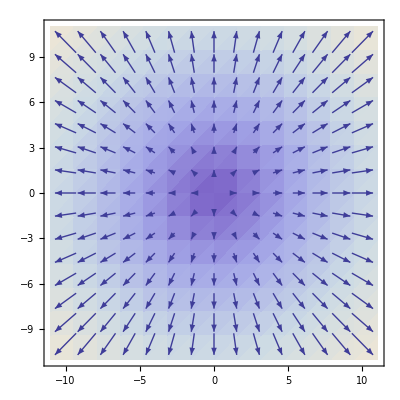

```mathematica
VectorDensityPlot[{x,y}, {x,-10,10}, {y,-10,10}]
```

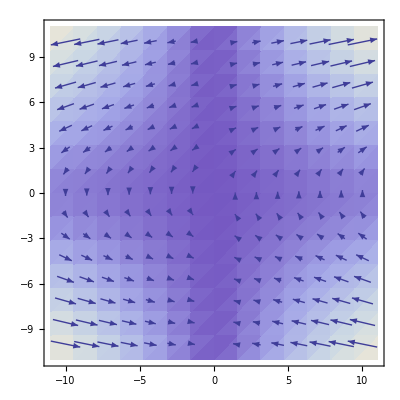

```mathematica
VectorDensityPlot[{x y, 2x}, {x,-10,10}, {y,-10,10}]
```

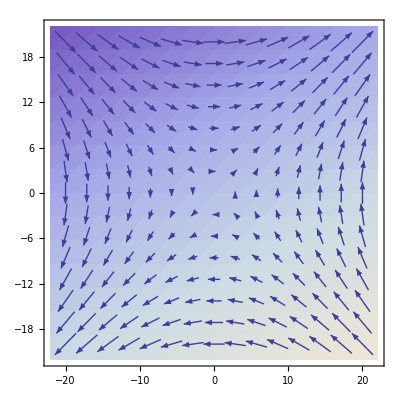

```mathematica
VectorDensityPlot[{{y, x}, x-2 y}, {x, -20, 20}, {y, -20, 20}]
```

```mathematica
VectorDensityPlot[{x, - y}, {x, -20, 20}, {y, -20, 20}]
```

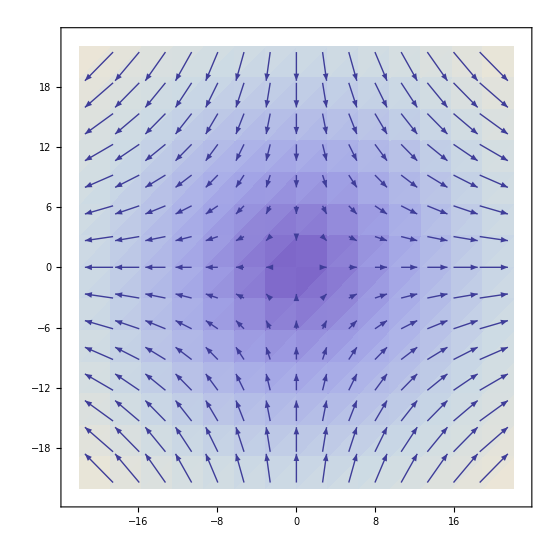

```mathematica
VectorDensityPlot[{x, 2e^(2x)}, {x, -20, 20}]
```

VectorDensityPlot::argrx: VectorDensityPlot called with 2 arguments; 3 arguments are expected.

```mathematica
VectorDensityPlot[{x,2  Exp[2 x]},{x,-20,20}]
```

VectorDensityPlot::argrx: VectorDensityPlot called with 2 arguments; 3 arguments are expected.

VectorDensityPlot[{x,2 Exp[2 x]},{x,-20,20}]

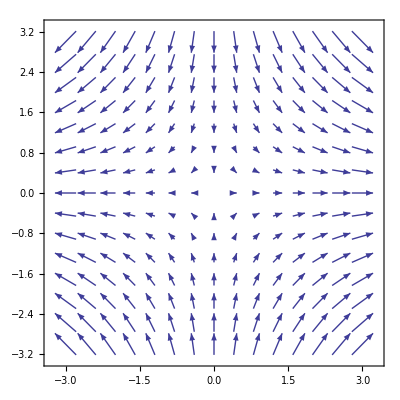

```mathematica
VectorPlot[{x, -y}, {x, -3, 3}, {y, -3, 3}]
```

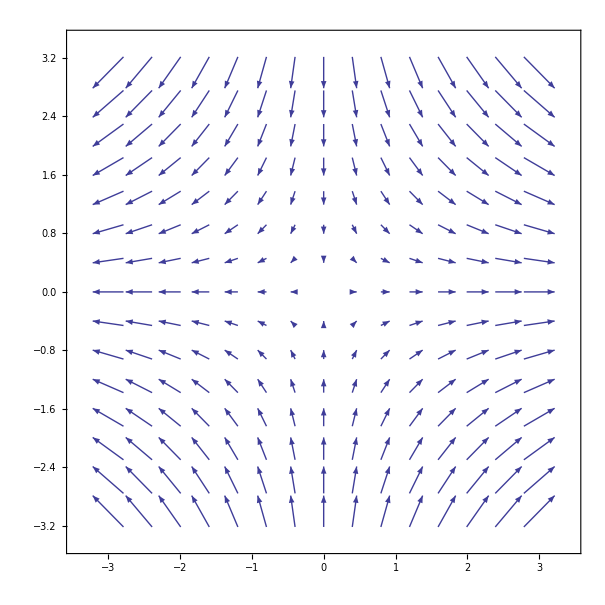

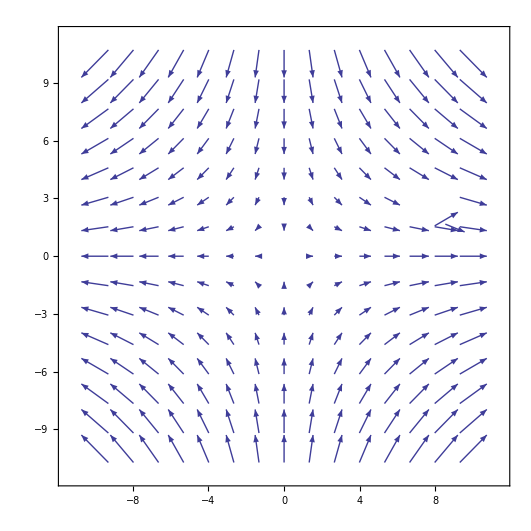

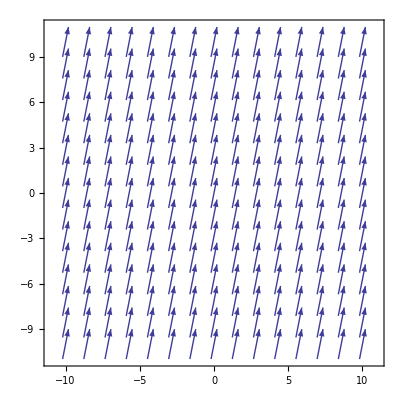

```mathematica
VectorPlot[{1, 5}, {x, -10, 10}, {y, -10, 10}]
```

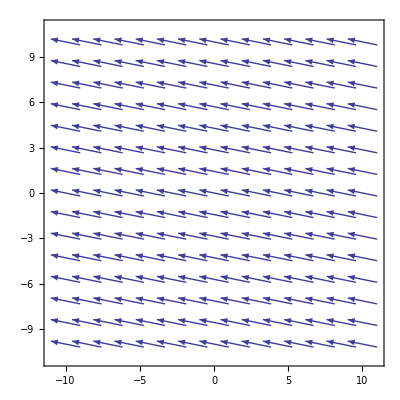

```mathematica
VectorPlot[{-1, 1/5}, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
DSolve[y'[x] == x ]
```

DSolve::argmu: DSolve called with 1 argument; 3 or more arguments are expected.

```mathematica
DSolve[y'[x]==x, x]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
DSolve[y'[x]==-y[x]/x, y[x], x]
```

```mathematica
{{y[x]->C[1]/x}}
DSolve[y'[x] == x, y[x], x]
```

{{y[x]→C[1]/x}}

```mathematica
{{y[x]->x^2/2+C[1]}}
Clear[y]
DSolve[{y'[x]==-y[x]/x, y[1] == 1}, y[x], x]
```

{{y[x]→x^2/2+C[1]}}

```mathematica
d1 = {{y[x]->1/x}}
```

{{y[x]→1/x}}

```mathematica
DSolve[{y'[x]==1, y[1] == 1}, y[x], x]
```

{{y[x]→x}}

```mathematica
DSolve[{y'[x]==-x/y[x], y[0] == 1}, y[x], x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

```mathematica
{{y[x]->√(1-x^2)}}
Plot[d1, {x, -3, 3} ]
```

{{y[x]→√(1-x^2)}}

-Graphics-

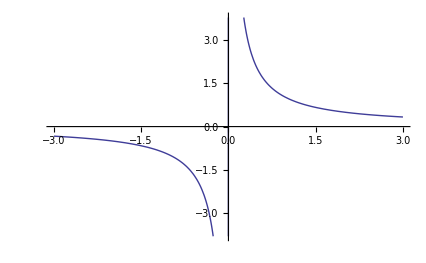

```mathematica
p1 = Plot[y[x]/.d1, {x, -3, 3}]
```

```mathematica
p1
```

```mathematica
p1
```

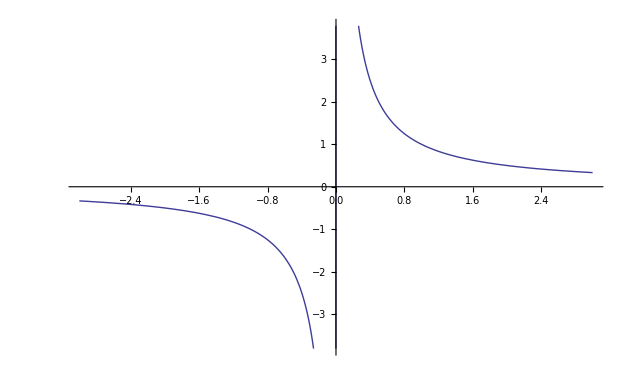
```mathematica
-Graphics-
Show[p1, d1]
```

-Graphics-

-Graphics-